Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

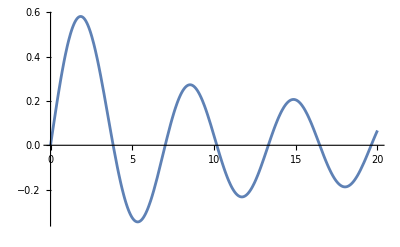

{x→0.}

{x→3.83171}

{x→7.01559}

```mathematica
g[x_]:= BesselJ[1,x]
Plot[g[x], {x,0,20}]
z1=FindRoot[g[x],{x,0.1}]
z2=FindRoot[g[x],{x,4}]
z3=FindRoot[g[x],{x,7.5}]
```

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
h[x_]:= Sin[x] Exp[-x]
Integrate[h[x],x]
D[%,x]
Simplify[%]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

ⅇ^-x Sin[x]

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

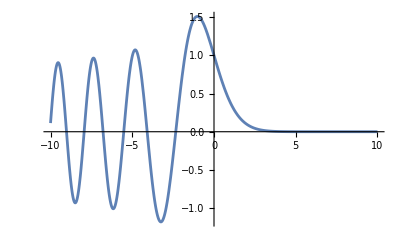

```mathematica
c= -3^(1/3) Gamma[2/3] / Gamma[1/3];
sol1 = DSolve[{y''[x]-x y[x]==0,y[0]==1,  y'[0]==c},y[x],x]
Plot[Evaluate[y[x]/. sol1],{x,-10,10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

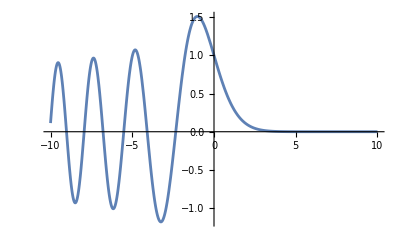

```mathematica
c= -3^(1/3) Gamma[2/3] / Gamma[1/3];
sol2 = NDSolve[{y''[x]-x y[x]==0,y[0]==1,  y'[0]==c},y[x],{x,-10,10},AccuracyGoal->13,PrecisionGoal->13]
Plot[Evaluate[y[x]/. sol2],{x,-10,10}]
```

Plot them togheter

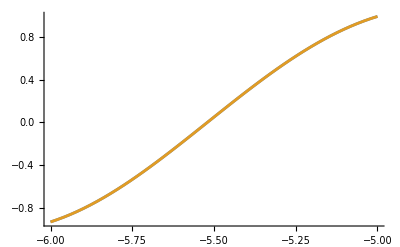

```mathematica
Plot[{Evaluate[y[x]/. sol1],Evaluate[y[x]/. sol2]},{x,-6,-5}]
```